```mathematica
(****************************)
(**    DATA PREPARATION    **)
(****************************)
(* Retrieve raw data  from
 https://github.com/pcm-dpc/COVID-19/blob/master/dati-andamento-nazionale/dpc-covid19-ita-andamento-nazionale.csv
and save as "data_it.csv"   *)
filedata="data_it.csv";
dataraw=Import[filedata,"CSV"];
n=Length[dataraw];
nf=Length[Flatten[dataraw]]/n;
data=Table[If[j==2,i-7,dataraw[[i,j]]],{i,2,n},{j,2,nf-2}];
n=Length[data];
nf=Length[data[[1]]];
Print[" Number of fields:  ",nf, "\n"," Number of days:    ",n]
(**  
i = 1,...,n    gives the day, (i-6) of March, running from Feb 24 to March (n-6);

  j = 1,...,12,  gives the field:   1 = "giorno di Marzo",   2 = "ricoverati con sintomi",   3 = "terapia intensiva",   4 = "tot ospedalizzati",   5 = "isolamento domiciliare",
  6 = "totale positivi",  7 = "variazione_totale_positivi",   8 = "nuovi_positivi",   9 = "dimessi_guariti",   10 = "deceduti",   11 = "totale_casi",  12 = "tamponi".

Obviously:      #4 = #3 + #2 ,    #6 = #5 + #4 ,    #6[[i]] = #6[[i-1]] + #7[[i]] ,   #11 = #6 + #9 + #10 ,
**)


(**
NB:       Data of 10 (i=16) are affected by a  known bug: due to some technical problem, Lombardia region data of 10 March for newly  infected people (650 confirmed cases) (j=7)  were accounted for only on 11 March. It is thus necessary to add 650 to entries in columns
 5, 6, 7, 11, of 10 March, and to substract 650 from column 7 of 11 March (line 16 and 17, respectively).
**)
data=Table[If [i==16,data[[i,j]]+Which[j==5,650,j==6,650,j==7,650,j==11,650,True,0],data[[i,j]]],{i,1,n},{j,1,nf}];
data=Table[If[i==17 && j==7, data[[i,j]]-650,data[[i,j]]],{i,1,n},{j,1,nf}];
(**    For all data, we assume that data of magnitude " n "   is affected by an error  " +/- Sqrt[n] "    **)
datapm=Table[If[j==1,data[[i,j]],Around[data[[i,j]],Sqrt[data[[i,j]]]]],{i,1,n},{j,1,nf}];
```

Number of fields:  12
 Number of days:    39

```mathematica
(**  Each time, we discard the last, say, `ncheck' days for the fit, to use them as a test of the prediciive power of the various models  **)
n=39
ncheck=7
nfit=n-ncheck
```

39

7

32

figCC_26_7.png

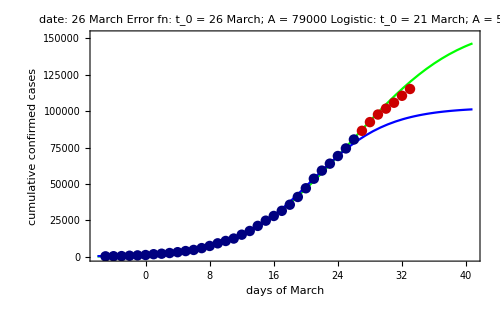

```mathematica
(********************************************************************)
(**  CUMULATED CONFIRMED CASES ;  best fit of error vs logistic fn  **)
(********************************************************************)
figname=StringJoin["figCC_",ToString[nfit-6],"_",ToString[ncheck],".png"]
(************************************************************************************************************************************)
dataCC=Table[{data[[i,1]],data[[i,11]]},{i,1,n}];
dataCCpm=Table[{data[[i,1]],Around[data[[i,11]],  Sqrt[data[[i,11]]]]},{i,1,n}];
(** Fit with Erf and Logistic  **)
datafit=Table[dataCC[[i]],{i,1,nfit}];
dataplot=Table[dataCCpm[[i]],{i,1,nfit}];
datacheck=Table[dataCCpm[[i]],{i,nfit+1,n}];
weights=Table[1/(dataCCpm[[i,2,2]])^2,{i,1,nfit}];

fitCCa1=NonlinearModelFit[datafit,a (1+Erf[b(t-t0)]), {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
fitCCa2=NonlinearModelFit[datafit,a /(1+ Exp[-b (t -t0)]), {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
(**************)
param1=fitCCa1["BestFitParameters"];
asymp1= a/.param1[[1]];
inflecdate1=t0/.param1[[3]];
param2=fitCCa2["BestFitParameters"];
asymp2= .5 a/.param2[[1]];
inflecdate2=t0/.param2[[3]];
datadate=nfit-6;
(**  Labels  **)
preparelabel[inflecdate_,asymp_]:= StringJoin["t_0 = ",ToString[Round[inflecdate]]," March; A = ",ToString[Round[asymp,1000]]]
plotlabel= StringJoin["date: ",ToString[datadate]," March"];
plotlabel1= preparelabel[inflecdate1,asymp1];
plotlabel2= preparelabel[inflecdate2,asymp2];
plotlabeltot=StringJoin["        ",plotlabel,"\n Error fn: ",plotlabel1,"\n Logistic: ",plotlabel2] ;
(**   Plot   **)
range=1.2;
rangey= 1.1dataCC[[n,2]]range;
rangex=(n-5)range;
p0f=ListPlot[dataplot,IntervalMarkers->"Bars",AxesOrigin->{-6,0},PlotStyle->{PointSize[0.015],Darker[Blue,.5],Thickness[0.003]},PlotRange->{{-6,rangex},{0,rangey}}];
p0c=ListPlot[datacheck,IntervalMarkers->"Bars",PlotStyle->{PointSize[0.015],Darker[Red,.2],Thickness[0.003]}];p12=Plot[{fitCCa1[x],fitCCa2[x]},{x,-6,rangex},PlotStyle-> {Green,Blue},PlotRange->{{-6,rangex},{0,rangey}},Frame->True,FrameLabel->{"days of March","cumulative confirmed cases"},PlotLabel->Style[Framed[plotlabeltot]]];
ppp=Show[p12,p0f,p0c]
Export[figname,ppp,ImageResolution->300];
```

figCF_26_7.png

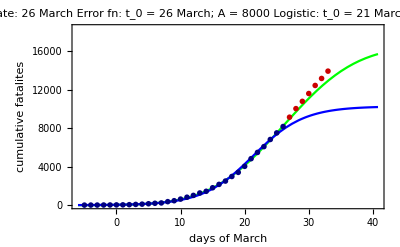

```mathematica
(********************************************************************)
(**  CUMULATED FATALITIES ;  best fit of error vs logistic fn       **)
(********************************************************************)
figname=StringJoin["figCF_",ToString[nfit-6],"_",ToString[ncheck],".png"]
(************************************************************************************************************************************)
dataCF=Table[{data[[i,1]],data[[i,10]]},{i,1,n}];
dataCFpm=Table[{data[[i,1]],Around[data[[i,10]],  Sqrt[data[[i,10]]]]},{i,1,n}];
(** Fit with Erf and Logistic  **)
datafit=Table[dataCF[[i]],{i,1,nfit}];
dataplot=Table[dataCFpm[[i]],{i,1,nfit}];
datacheck=Table[dataCFpm[[i]],{i,nfit+1,n}];
weights=Table[1/(dataCFpm[[i,2,2]])^2,{i,1,nfit}];

fitCFa1=NonlinearModelFit[datafit,a (1+Erf[b(t-t0)]), {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
fitCFa2=NonlinearModelFit[datafit,a /(1+ Exp[-b (t -t0)]), {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
(**************)
param1=fitCFa1["BestFitParameters"];
asymp1= a/.param1[[1]];
inflecdate1=t0/.param1[[3]];
param2=fitCFa2["BestFitParameters"];
asymp2= .5 a/.param2[[1]];
inflecdate2=t0/.param2[[3]];
datadate=nfit-6;
(**  Labels  **)
preparelabel[inflecdate_,asymp_]:= StringJoin["t_0 = ",ToString[Round[inflecdate]]," March; A = ",ToString[Round[asymp,1000]]]
plotlabel= StringJoin["date: ",ToString[datadate]," March"];
plotlabel1= preparelabel[inflecdate1,asymp1];
plotlabel2= preparelabel[inflecdate2,asymp2];
plotlabeltot=StringJoin["        ",plotlabel,"\n Error fn: ",plotlabel1,"\n Logistic: ",plotlabel2] ;
(**   Plot   **)
range=1.2;
rangey= 1.1dataCF[[n,2]]range;
rangex=(n-5)range;
p0f=ListPlot[dataplot,IntervalMarkers->"Bars",AxesOrigin->{-6,0},PlotStyle->{PointSize[0.01],Darker[Blue,.5],Thickness[0.003]},PlotRange->{{-6,rangex},{0,rangey}}];
p0c=ListPlot[datacheck,IntervalMarkers->"Bars",PlotStyle->{PointSize[0.01],Darker[Red,.2],Thickness[0.003]}];p12=Plot[{fitCFa1[x],fitCFa2[x]},{x,-6,rangex},PlotStyle-> {Green,Blue},PlotRange->{{-6,rangex},{0,rangey}},Frame->True,FrameLabel->{"days of March","cumulative fatalites"},PlotLabel->Style[Framed[plotlabeltot]]];
ppp=Show[p12,p0f,p0c]
Export[figname,ppp,ImageResolution->300];
```

figDI_26_7.png

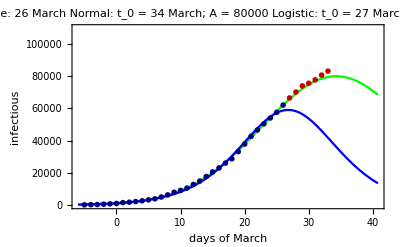

```mathematica
(**************************************************************)
(**   INFECTIOUS ;  best fit of normal vs logistic distrib.   **)
(**************************************************************)
figname=StringJoin["figDI_",ToString[nfit-6],"_",ToString[ncheck],".png"]
(************************************************************************************************************************************)
dataDI=Table[{data[[i,1]],data[[i,6]]},{i,1,n}];
dataDIpm=Table[{data[[i,1]],Around[data[[i,6]],  Sqrt[data[[i,6]]]]},{i,1,n}];
(** Fit with Normal and Logistic  **)
datafit=Table[dataDI[[i]],{i,1,nfit}];
dataplot=Table[dataDIpm[[i]],{i,1,nfit}];
datacheck=Table[dataDIpm[[i]],{i,nfit+1,n}];
weights=Table[1/(dataDIpm[[i,2,2]])^2,{i,1,nfit}];

fitDIa1=NonlinearModelFit[datafit,a Exp[-b(t-t0)^2], {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
fitDIa2=NonlinearModelFit[datafit,a  Exp[-b (t -t0)]/(1+ Exp[-b (t -t0)])^2, {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
(**************)
param1=fitDIa1["BestFitParameters"];
peak1=a/.param1[[1]];
peakdate1=t0/.param1[[3]];
param2=fitDIa2["BestFitParameters"];
peak2= (a/.param2[[1]])/4;
peakdate2=t0/.param2[[3]];
datadate=nfit-6;
(**  Labels  **)
preparelabel[inflecdate_,asymp_]:= StringJoin["t_0 = ",ToString[Round[inflecdate]]," March; A = ",ToString[Round[asymp,1000]]]
plotlabel= StringJoin["date: ",ToString[datadate]," March"];
plotlabel1= preparelabel[peakdate1,peak1];
plotlabel2= preparelabel[peakdate2,peak2];
plotlabeltot=StringJoin["        ",plotlabel,"\n","  Normal: ",plotlabel1,"\n"," Logistic:  ",plotlabel2] ;
(**   Plot   **)
range=1.2;
rangey= 1.1dataDI[[n,2]]range;
rangex=(n-5)range;
p0f=ListPlot[dataplot,IntervalMarkers->"Bars",AxesOrigin->{-6,0},PlotStyle->{PointSize[0.01],Darker[Blue,.5],Thickness[0.003]},PlotRange->{{-6,rangex},{0,rangey}}];
p0c=ListPlot[datacheck,IntervalMarkers->"Bars",PlotStyle->{PointSize[0.01],Darker[Red,.2],Thickness[0.003]}];p12=Plot[{fitDIa1[x],fitDIa2[x]},{x,-6,rangex},PlotStyle-> {Green,Blue},PlotRange->{{-6,rangex},{0,rangey}},Frame->True,FrameLabel->{"days of March","infectious"},PlotLabel->Style[Framed[plotlabeltot]]];
ppp=Show[p12,p0f,p0c]
Export[figname,ppp,ImageResolution->300];
```

figDF_26_7.png

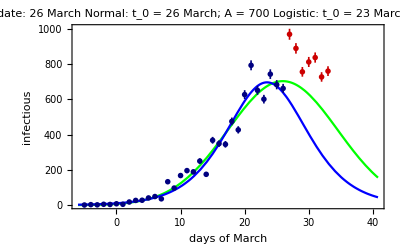

```mathematica
(********************************************************************)
(**   DAILY FATALITIES ;  best fit of normal vs logistic distrib.   **)
(********************************************************************)
figname=StringJoin["figDF_",ToString[nfit-6],"_",ToString[ncheck],".png"]
(************************************************************************************************************************************)
dataDF=Table[{data[[i,1]],If[i==1,data[[i,10]]-6,data[[i,10]]-data[[i-1,10]]]},{i,1,n}];
dataDFpm=Table[{data[[i,1]],Around[dataDF[[i,2]],  Sqrt[dataDF[[i,2]]]]},{i,1,n}];
(** Fit with Normal and Logistic  **)
datafit=Table[dataDF[[i]],{i,1,nfit}];
dataplot=Table[dataDFpm[[i]],{i,1,nfit}];
datacheck=Table[dataDFpm[[i]],{i,nfit+1,n}];
weights=Table[1/(dataDFpm[[i,2,2]])^2,{i,1,nfit}];

fitDFa1=NonlinearModelFit[datafit,a Exp[-b(t-t0)^2], {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
fitDFa2=NonlinearModelFit[datafit,a  Exp[-b (t -t0)]/(1+ Exp[-b (t -t0)])^2, {{a, 100000},{b,1},{t0,10}},t,
Weights->weights];
(**************)
param1=fitDFa1["BestFitParameters"];
peak1=a/.param1[[1]];
peakdate1=t0/.param1[[3]];
param2=fitDFa2["BestFitParameters"];
peak2= (a/.param2[[1]])/4;
peakdate2=t0/.param2[[3]];
datadate=nfit-6;
(**  Labels  **)
preparelabel[inflecdate_,asymp_]:= StringJoin["t_0 = ",ToString[Round[inflecdate]]," March; A = ",ToString[Round[asymp,100]]]
plotlabel= StringJoin["date: ",ToString[datadate]," March"];
plotlabel1= preparelabel[peakdate1,peak1];
plotlabel2= preparelabel[peakdate2,peak2];
plotlabeltot=StringJoin["        ",plotlabel,"\n","  Normal: ",plotlabel1,"\n"," Logistic:  ",plotlabel2] ;
(**   Plot   **)
range=1.2;
rangey= 1.1dataDF[[n,2]]range;
rangex=(n-5)range;
p0f=ListPlot[dataplot,IntervalMarkers->"Bars",AxesOrigin->{-6,0},PlotStyle->{PointSize[0.01],Darker[Blue,.5],Thickness[0.003]},PlotRange->{{-6,rangex},{0,rangey}}];
p0c=ListPlot[datacheck,IntervalMarkers->"Bars",PlotStyle->{PointSize[0.01],Darker[Red,.2],Thickness[0.003]}];p12=Plot[{fitDFa1[x],fitDFa2[x]},{x,-6,rangex},PlotStyle-> {Green,Blue},PlotRange->{{-6,rangex},{0,rangey}},Frame->True,FrameLabel->{"days of March","infectious"},PlotLabel->Style[Framed[plotlabeltot]]];
ppp=Show[p12,p0f,p0c]
Export[figname,ppp,ImageResolution->300];
```

```mathematica
(*******************************************************************************************)
(*******************************   That's all folks   **************************************)
(*******************************************************************************************)
```